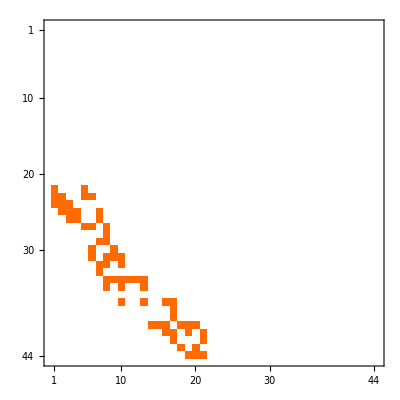

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
H=9;
W=5;
AH=ToeplitzMatrix[{1,1}~Join~Table[0,H-2]];
AW=ToeplitzMatrix[{1,1}~Join~Table[0,W-2]];
P=KroneckerProduct[AH,AW];
(*v=Array[vv,H*W];*)
v = RandomChoice[{0,1},Length@P];

analytic=Table[v[[i]]*(1-v[[j]])*P[[i,j]],{i,H*W},{j,H*W}];
analytic[[PermutationList@FindPermutation[v],PermutationList@FindPermutation[v]]]//MatrixPlot
(*simulated=DiagonalMatrix[v].P.DiagonalMatrix[1-v];
analytic==simulated
P.Flatten[Array[b,{H,W}]]==Flatten[ListConvolve[Table[1,3,3],ArrayPad[Array[b,{H,W}],1]]]*)
```

```mathematica
v
```

{0,0,0,0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,1,1,0,0,0,1,1,1,0,0,0,0,1,1,1,1}

```mathematica
Ordering[v]
PermutationList@FindPermutation[v]
```

{1,2,3,4,7,8,10,13,15,18,20,21,22,23,25,28,32,33,34,38,39,40,41,5,6,9,11,12,14,16,17,19,24,26,27,29,30,31,35,36,37,42,43,44,45}

{1,2,3,4,7,8,10,13,15,18,20,21,22,23,25,28,32,33,34,38,39,40,41,5,6,9,11,12,14,16,17,19,24,26,27,29,30,31,35,36,37}

```mathematica
N[1-Binomial[7,1]/Binomial[8,1]]
```

0.125

```mathematica
N@Mean@Select[Tuples[{0,1},14],(Total[#[[1;;8]]]==1)∧(Total[#[[7;;]]]==3)&]//Column
```

0.133333
0.133333
0.133333
0.133333
0.133333
0.133333
0.1
0.1
0.466667
0.466667
0.466667
0.466667
0.466667
0.466667

```mathematica
{1,2,3,4,5,6}[[2;;4]]
```

{2,3,4}